{{y[x]→(8.65956×10^-17+0.707107 ⅈ) ((1.+0. ⅈ) ParabolicCylinderD[-3.,(0.+1.41421 ⅈ) x]+(0.626657+0. ⅈ) ParabolicCylinderD[2.,1.41421 x])}}

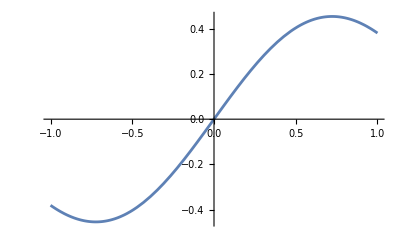

```mathematica
sol=DSolve[{(-0.5)*y''[x]+(0.5*x*x-5/2)*y[x]==0,y[0]==0,y'[0]==1},y[x],x]
Plot[Evaluate[y[x]/. sol],{x,-1,1}]
```